```mathematica
Quit[]
```

## Init

```mathematica
SetDirectory[NotebookDirectory[]];
list=Join[{"0.0"},Join[Table[ToString[SetPrecision[x,1]],{x,0.1,0.9,0.1}],Table[ToString[SetPrecision[x,2]],{x,1.1,2.0,0.1}]]];
```

```mathematica
Do[signal[x]=Import["data/RUNS_INI_SM/ggZZ4l_lo_mstw8lo_0.50_0.50_125_13T_"<>x<>".dat"],{x,list}]
signal["1.0"]=Import["data/RUNS_INI_SM/ggZZ4l_lo_mstw8lo_0.50_0.50_125_13T_1.0.dat"];
background["0.0"]=Import["data/RUNS_INI_SM/ZZlept_lo_mstw8lo_0.50_0.50_13T_BKG.dat"];
```

```mathematica
fact=3000*2*2*0.95^4;
factB=3000*1.7*2*0.95^4;
```

```mathematica
sortBC[list_?MatrixQ,dir:_Integer|{__Integer},priority_: {}]:=Module[{l=Length@list[[1,All]],w,p,d},w=Reverse@Range@l;
p=If[Length@priority>0,PadRight[Flatten@{priority},l],p=Range@l];
w=w[[Ordering@p]];
d=PadRight[Flatten@{dir},l];
Sort[list,NonNegative@Total[(w d MapThread[Order,{##}])]&]]
```

```mathematica
ListFunction[set_,min_,max_,i_,fact_]:=Flatten[set[i][[min;;max]][[All,1;;2]]/.{x_,y_}->{{x-0.025,fact y},{x+0.025,fact y}},1]
InterpFunction[set_,min_,max_,i_,fact_]:=Flatten[set[i][[min;;max]][[All,1;;2]]/.{x_,y_}->{{x-0.0249999999,fact y},{x+0.0249999999,fact y}},1]
```

```mathematica
PlotFunction[min_,max_,type_]:=GraphicsGrid[Table[ParallelTable[ListLogPlot[{ListFunction[signal,min,max,i,fact],ListFunction[signal,min,max,"1.0",fact],ListFunction[background,min-4,max-4,"0.0",factB],{{0,1/0.05},{1,1/0.05}}},Joined->True,InterpolationOrder->0,Frame->True,PlotStyle->Thick,PlotLabel->type<>" c_t = "<>ToString[i],ImageSize->{300,225},FrameLabel->{"D","N_Events/Bin"},PlotRange->{{0,1},Automatic}],{i,list[[5j+1;;5+5j]]}],{j,0,3}]]
```

```mathematica
plotDetails:=GraphicsRow[{ListLogPlot[Table[{i,ffSM[i]/ffBKG[i]},{i,0.05,0.95,0.05}],PlotRange->All,Joined->True,PlotRange->{{0.05,0.95},Automatic},Frame->True,GridLines->All,PlotStyle->Thick,FrameLabel->{"D","S/B"},ImageSize->{300,225}],ListLogPlot[{Table[{i,ffSM[i]},{i,0.05,0.95,0.05}],Table[{i,ffBKG[i]},{i,0.05,0.95,0.05}],{{0.05,1},{0.95,1}}},PlotRange->All,Joined->True,Frame->True,GridLines->All,PlotStyle->Thick,PlotRange->{{0.05,0.95},Automatic},FrameLabel->{"D","N_signal & N_back"}]}]
```

## Plots

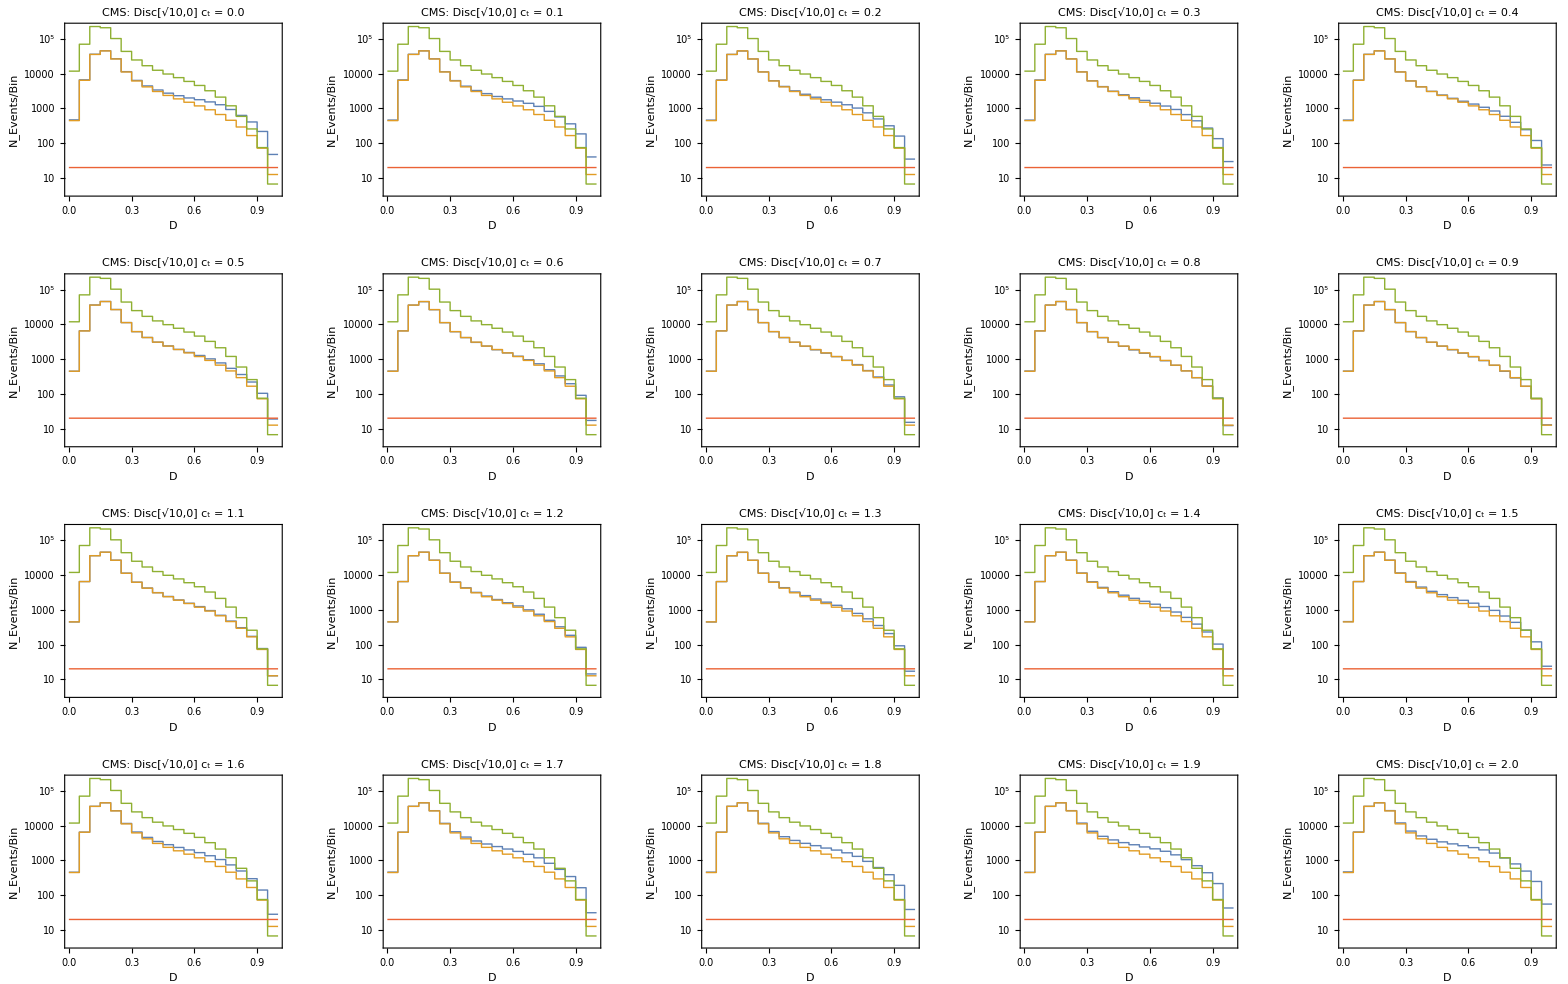

```mathematica
PlotFunction[179,198,"CMS: Disc[√10,0]"]
```

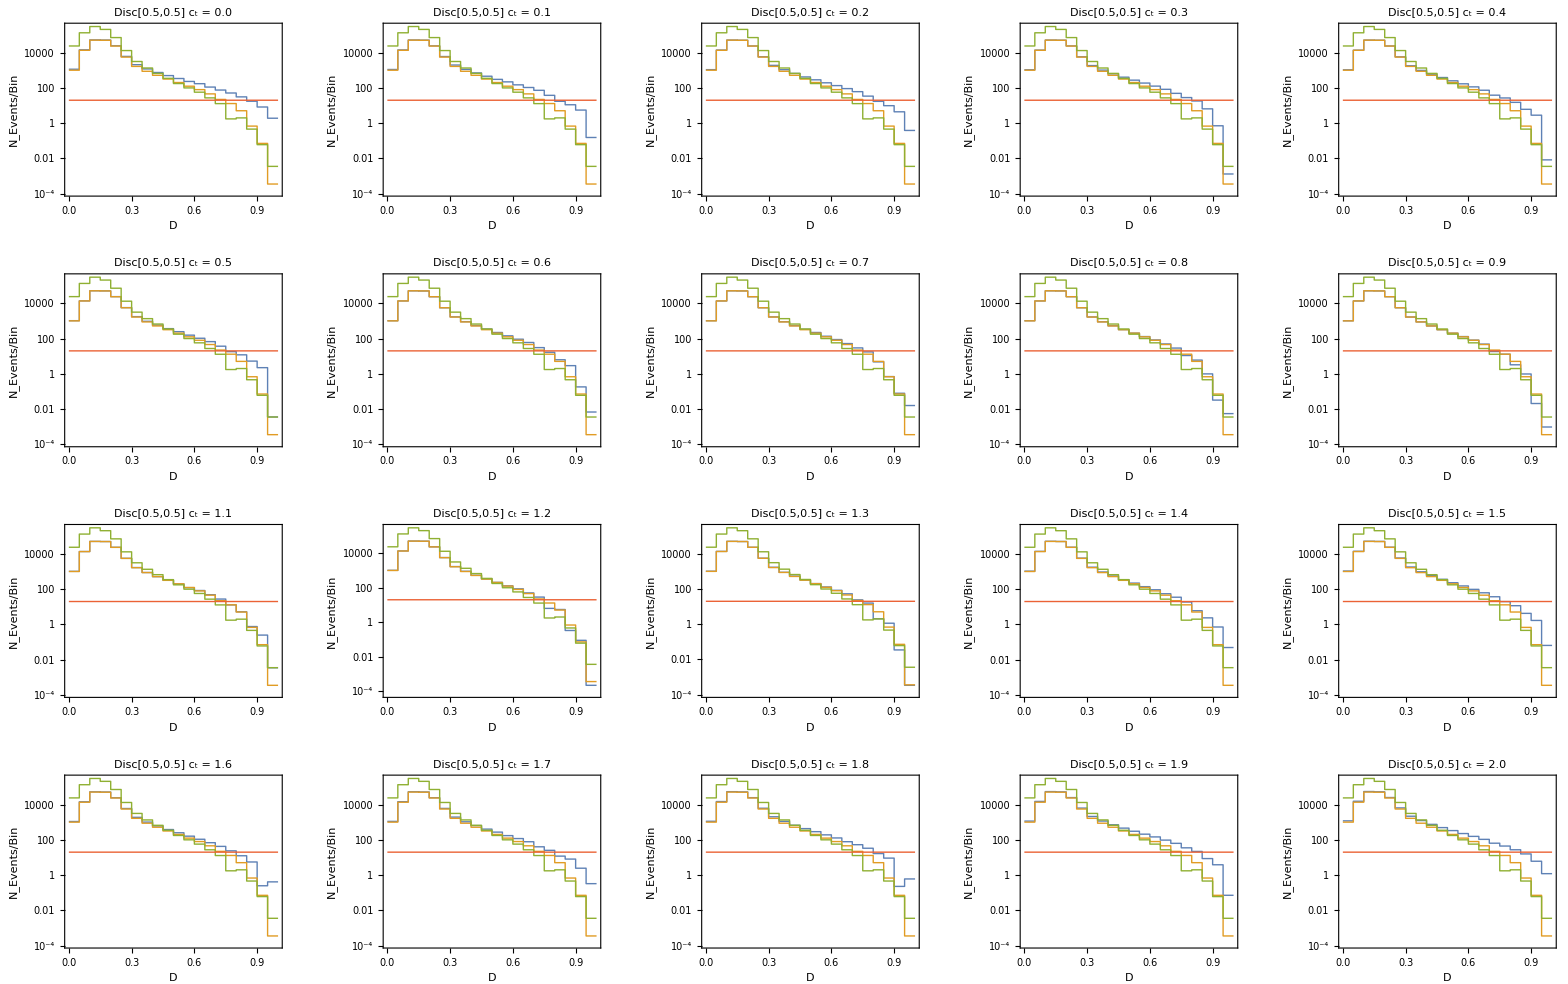

```mathematica
PlotFunction[207,226,"Disc[0.5,0.5]"]
```

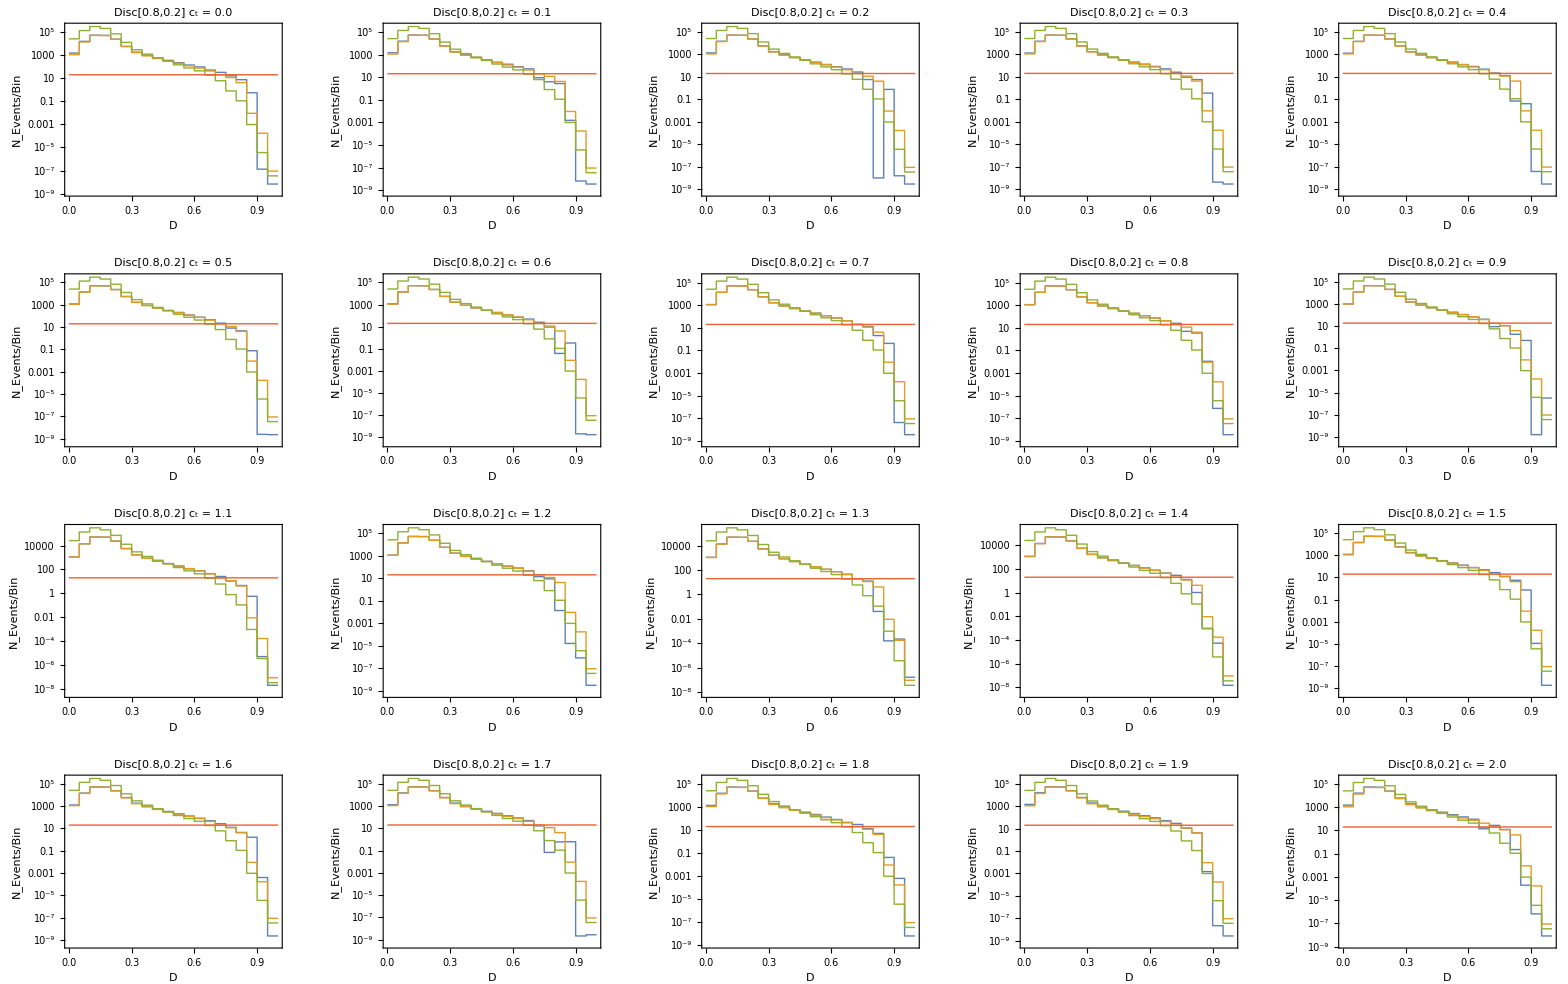

```mathematica
PlotFunction[235,254,"Disc[0.8,0.2]"]
```

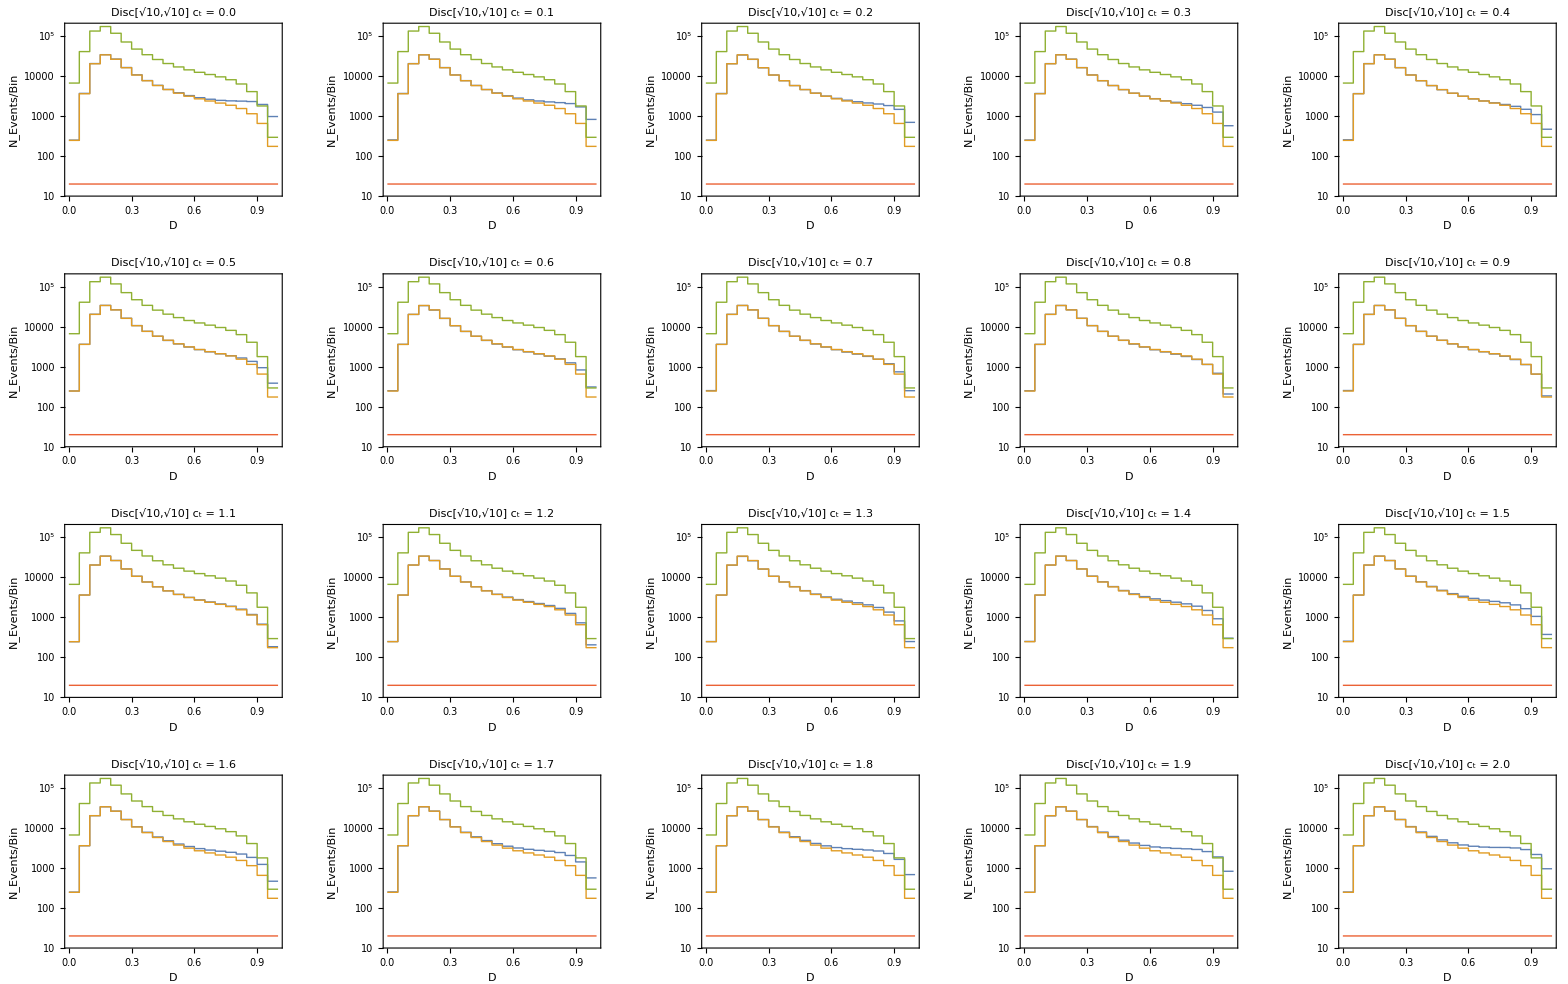

```mathematica
PlotFunction[263,282,"Disc[√10,√10]"]
```

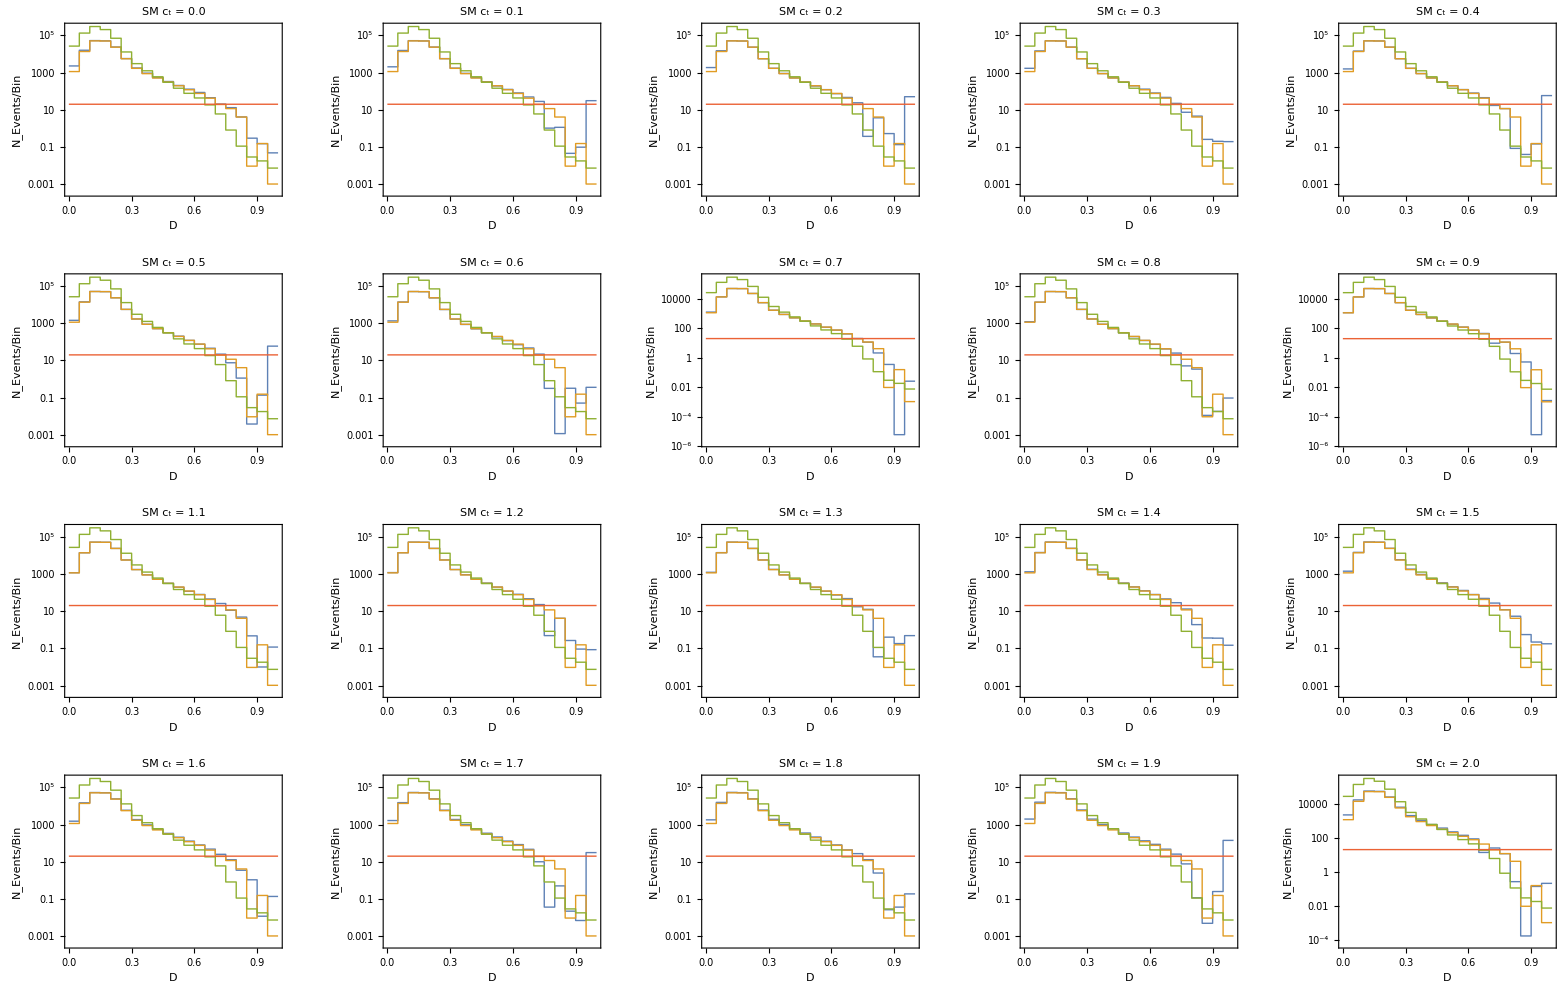

```mathematica
PlotFunction[291,310,"SM"]
```

## the analysis

### CMS discriminator

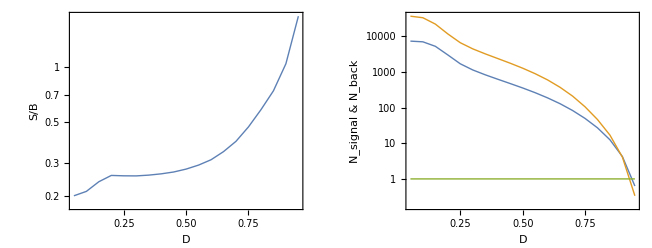

```mathematica
ff[Dcut_]:=Interpolation[Table[{ToExpression[i],NIntegrate[Interpolation[InterpFunction[signal,179,198,i,fact],InterpolationOrder->0][x],{x,Dcut,0.999999999}]},{i,Join[{"1.0"},list]}]]
ffSM[Dcut_]:=NIntegrate[Interpolation[InterpFunction[signal,179,198,"1.0",fact],InterpolationOrder->0][x],{x,Dcut,0.999999999}]
ffBKG[Dcut_]:=NIntegrate[Interpolation[InterpFunction[background,175,194,"0.0",factB],InterpolationOrder->0][x],{x,Dcut,0.999999999}]
chiSqG[Dcut_,x_]:=(ff[Dcut][x]-ffSM[Dcut])^2/ffBKG[Dcut]
plotDetails
```

```mathematica
p1=Plot[chiSqG[0.6,ct],{ct,0.,2.}];
p0=Plot[{1,2,3},{x,0.,2.},PlotRange->{{0.2,1.8},{0,4}},Frame->True];
```

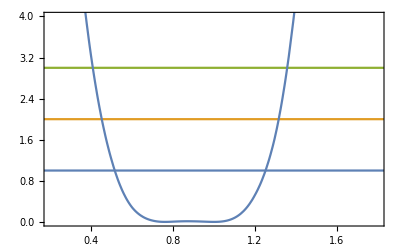

```mathematica
Show[p0,p1]
```

### 0.5-0.5 discriminator

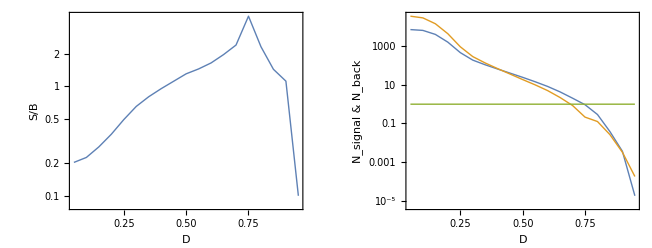

```mathematica
Clear[ff,ffSM,ffBKG,chiSqG,p1,p0]
ff[Dcut_]:=Interpolation[Table[{ToExpression[i],NIntegrate[Interpolation[InterpFunction[signal,207,226,i,fact],InterpolationOrder->0][x],{x,Dcut,0.999999999}]},{i,Join[{"1.0"},list]}]]
ffSM[Dcut_]:=NIntegrate[Interpolation[InterpFunction[signal,207,226,"1.0",fact],InterpolationOrder->0][x],{x,Dcut,0.999999999}]
ffBKG[Dcut_]:=NIntegrate[Interpolation[InterpFunction[background,203,222,"0.0",factB],InterpolationOrder->0][x],{x,Dcut,0.999999999}]
chiSqG[Dcut_,x_]:=(ff[Dcut][x]-ffSM[Dcut])^2/ffBKG[Dcut]
plotDetails
```

```mathematica
p1=Plot[chiSqG[0.4,ct],{ct,0.,2.}];
p0=Plot[{1,2,3},{x,0.,2.},PlotRange->{{0.2,1.8},{0,4}},Frame->True];
```

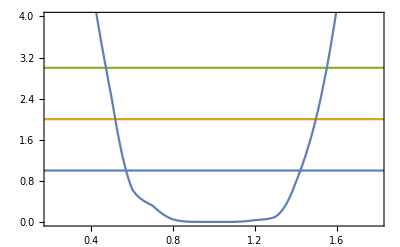

```mathematica
Show[p0,p1]
```

### 0.8-0.2 discriminator

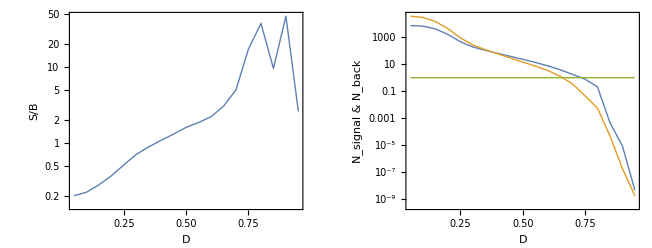

```mathematica
Clear[ff,ffSM,ffBKG,chiSqG,p1,p0]
ff[Dcut_]:=Interpolation[Table[{ToExpression[i],NIntegrate[Interpolation[InterpFunction[signal,235,254,i,fact],InterpolationOrder->0][x],{x,Dcut,0.999999999}]},{i,Join[{"1.0"},list]}]]
ffSM[Dcut_]:=NIntegrate[Interpolation[InterpFunction[signal,235,254,"1.0",fact],InterpolationOrder->0][x],{x,Dcut,0.999999999}]
ffBKG[Dcut_]:=NIntegrate[Interpolation[InterpFunction[background,231,250,"0.0",factB],InterpolationOrder->0][x],{x,Dcut,0.999999999}]
chiSqG[Dcut_,x_]:=(ff[Dcut][x]-ffSM[Dcut])^2/ffBKG[Dcut]
plotDetails
```

```mathematica
p1=Plot[chiSqG[0.45,ct],{ct,0.,2.}];
p0=Plot[{1,2,3},{x,0.,2.},PlotRange->{{0.2,1.8},{0,4}},Frame->True];
```

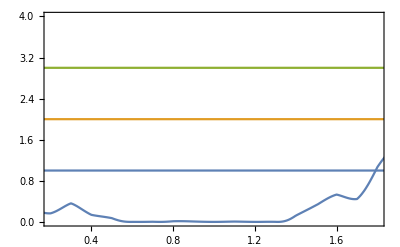

```mathematica
Show[p0,p1]
```

### √10-√10 discriminator

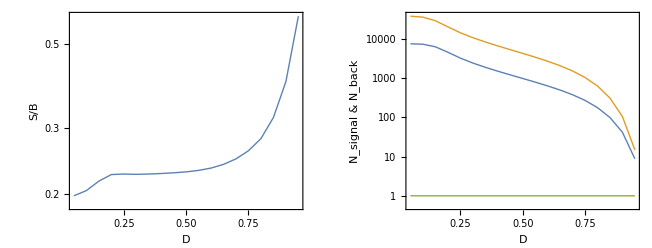

```mathematica
Clear[ff,ffSM,ffBKG,chiSqG,p1,p0]
ff[Dcut_]:=Interpolation[Table[{ToExpression[i],NIntegrate[Interpolation[InterpFunction[signal,263,282,i,fact],InterpolationOrder->0][x],{x,Dcut,0.999999999}]},{i,Join[{"1.0"},list]}]]
ffSM[Dcut_]:=NIntegrate[Interpolation[InterpFunction[signal,263,282,"1.0",fact],InterpolationOrder->0][x],{x,Dcut,0.999999999}]
ffBKG[Dcut_]:=NIntegrate[Interpolation[InterpFunction[background,259,278,"0.0",factB],InterpolationOrder->0][x],{x,Dcut,0.9999999}]
chiSqG[Dcut_,x_]:=(ff[Dcut][x]-ffSM[Dcut])^2/ffBKG[Dcut]
plotDetails
```

```mathematica
p1=Plot[chiSqG[0.95,ct],{ct,0.,2.}];
p0=Plot[{1,2,3},{x,0.,2.},PlotRange->{{0.2,1.8},{0,4}},Frame->True];
```

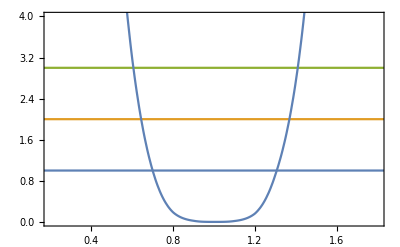

```mathematica
Show[p0,p1]
```

### SM discriminator

```mathematica
ffSM[0.45]
ffBKG[0.45]
```

39.1317

29.7126

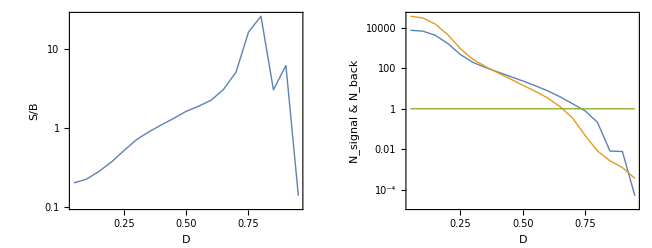

```mathematica
Clear[ff,ffSM,ffBKG,chiSqG,p1,p0]
ff[Dcut_]:=Interpolation[Table[{ToExpression[i],NIntegrate[Interpolation[InterpFunction[signal,291,310,i,fact],InterpolationOrder->0][x],{x,Dcut,0.999999999}]},{i,Join[{"1.0"},list]}]]
ffSM[Dcut_]:=NIntegrate[Interpolation[InterpFunction[signal,291,310,"1.0",fact],InterpolationOrder->0][x],{x,Dcut,0.999999999}]
ffBKG[Dcut_]:=NIntegrate[Interpolation[InterpFunction[background,287,306,"0.0",factB],InterpolationOrder->0][x],{x,Dcut,0.999999999}]
chiSqG[Dcut_,x_]:=(ff[Dcut][x]-ffSM[Dcut])^2/ffBKG[Dcut]
plotDetails
```

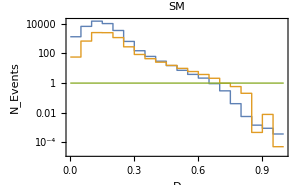

```mathematica
ListLogPlot[{ListFunction[background,291-4,310-4,"0.0",factB*0.05],ListFunction[signal,291,310,"1.0",fact*0.05],{{0,1},{1,1}}},Joined->True,InterpolationOrder->0,Frame->True,PlotStyle->Thick,PlotLabel->" SM ",ImageSize->{300,225},FrameLabel->{"D","N_Events"},PlotRange->{{0,1},Automatic}]
```

```mathematica
p1=Plot[chiSqG[0.4,ct],{ct,0.,2.}];
p0=Plot[{1,2,3},{x,0.,2.},PlotRange->{{0.2,1.8},{0,4}},Frame->True];
```

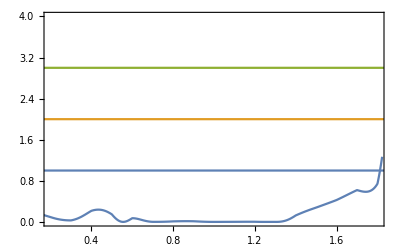

```mathematica
Show[p0,p1]
```